# Continuous Quantum Measurement, from Bayes' Rule to the Quantum Kalman Filter

In this computational essay, we explore a quantum particle whose position is monitored continuously. This is what is usually called continuous weak measurement. It starts from the stochastic Schrödinger equation (the SDE that drives a state while it is being measured), turns the measurement step into ordinary Bayesian updating, and runs the whole thing on a position grid with a Trotter-Suzuki splitting scheme. We focus on two examples in particular. A free particle, where the measurement narrows a spread-out state to a packet of finite steady width and the noisy measurement record alone tells you where it settled. And a harmonic trap, where continuous measurement squeezes the position variance below the ground state's, and the quantum Kalman filter that levitated-nanoparticle and membrane experiments actually run rebuilds the conditional mean position from the noisy signal.

Mads Bahrami. Last updated August 4, 2026.

## Part I: The Equation of Motion, and Measurement as Bayes' Rule

Start with the equation of motion. A particle with Hamiltonian Ĥ whose position is measured continuously and weakly obeys a stochastic Schrödinger equation (SSE), the diffusive quantum-state-diffusion form,

dψ=[-i/ℏ Ĥ dt-λ/2(x̂-⟨x̂⟩)^2 dt+√λ(x̂-⟨x̂⟩)dW]ψ.

In words: the first term is ordinary unitary evolution under Ĥ; the last is the stochastic measurement backaction, proportional to the Wiener increment dW (an independent Gaussian of mean zero and variance dt in each step), which nudges the state toward a sharper position; and the middle term is the nonlinear drift whose only job is to keep ψ normalized. The strength λ sets how fast position information arrives, and its dimensions (inverse length squared, per time) say what kind of rate it is: what accrues is not position but statistical distinguishability: the log-likelihood ratio between two candidate positions Δx apart grows at the rate 2λ(Δx)^2 (equivalently their Kullback-Leibler rate), a fact Part III will watch in action. (Factor conventions for λ and for the record differ across the literature by twos; translate parameters before comparing formulas across sources.) The detector's own output over the same increment is the measurement record

d Y_t=2 √λ ⟨x̂⟩_t dt+d W_t,

which is the conditional mean position ⟨x̂⟩ buried in white noise. Equivalently, the record is signal (the mean) plus shot noise (the same dW). Because that one increment drives both the state and the record, an observer who knows the initial state can feed the record into the same dynamics and track the conditional state as the experiment runs, never seeing the wavefunction directly. That is quantum filtering, and it is what a real experiment computes, in software, from the detector's streaming output. Part IV does it concretely, and there the record fixes the conditional mean while the width follows a rule that never looks at the record.

Keep one piece of bookkeeping straight from the start. In an experiment only the record is data; the conditional state, its mean, and its width are inferences from that data through an assumed model. In this essay even the record is synthetic, generated by the same equations that propagate the state, so whenever two of our computed objects agree below, the agreement is an internal consistency check of the model, never evidence for it. What evidence for the model itself looks like in a laboratory, whiteness tests on the filter's surprises and independent out-of-loop calibration, appears at the close of Part IV.

The above SSE is the dt→0 limit of a concrete two-step update, and it is the update, not the differential form, that the simulation runs. Over one step the detector returns a single weak-measurement outcome x̄, a reading of the position blurred by Gaussian noise, and the state is revised by Bayes' rule. The reading has likelihood

P(x̄|x)∝e^(-2λ dt (x-x̄)^2),

a Gaussian in x̄ centered on the candidate position x. (The dropped constant is √(2λ dt/π); it cancels in the normalized update below, and needs restoring only if P(x̄) is read as a normalized density rather than a reweighting factor.) Because the reading is noisy, the outcome is not drawn from (ψ(x))^2 directly but from the prior predictive P(x̄)=∫P(x̄|x) (ψ(x))^2 dx, the density (ψ(x))^2 convolved with the detector noise. And the conditional (posterior) density is the prior reweighted by the likelihood,

(ψ(x))^2 ⟶ (P(x̄|x) (ψ(x))^2)/(P(x̄)),

which is Bayes' rule verbatim: posterior ∝ likelihood × prior. At the level of amplitudes this reweighting is a Kraus operator M̂(x̄)∝e^(-λ dt (x̂-x̄)^2), the square root of the likelihood, applied and renormalized; multiplying each amplitude by √(P(x̄|x)) carries the phase along. The particle then evolves unitarily for the step, so one full step is Bayes' rule followed by Hamiltonian evolution:

ψ(t+dt)=(e^(-i Ĥ dt/ℏ)M̂(x̄)ψ(t))/(M̂(x̄)ψ(t)).

In short: measure by Bayes' rule, then evolve. (The ordering is a discretization, not physics: over a real interval the two proceed together, and splitting them costs an error first order in dt; Part III puts a number on it.) Notice the one fact we will lean on for the rest of the notebook: the measurement half of this update knows nothing about Ĥ. The outcome distribution, the Bayesian reweighting, and the renormalization are identical for a free particle or a trap; only the unitary e^(-i Ĥ dt/ℏ) carries the potential. So generalizing the simulation to any V(x) will mean generalizing that one factor and leaving the measurement untouched, which is exactly what the next Part does.

### Glossary

The symbols of this Part sort into what a detector records and what an observer infers from it. What a detector actually returns is finite, one number per time step Δt, so here we write those recorded increments with Δ; the continuous d-forms of the equations above (d Y_t, d W_t) are their Δt→0 idealizations, living only inside the model. The last column gives each symbol's standing: recorded, calibrated from the record, or inferred through the model.

Symbol | Meaning | Standing, and how it is checked
Δ Y_k | the measurement record over one step, Δ Y_k=2 √λ ⟨x̂⟩ Δt+Δ W_k | Recorded: the detector's output each step, the only raw data here.
(x̄)_k | one weak-measurement outcome per step, (x̄)_k=Δ Y_k/(2 √λ Δt) | Calibrated from the record, not a separate reading: the same Δ Y_k in position units. One reading is mostly noise.
⟨x̂⟩ | the conditional mean position, ∫x (ψ(x))^2 dx | Inferred: the filter of Part IV reconstructs it from the record, and feedback acts on it.
Δ W_k | the shot-noise increment (variance Δt), the record minus the mean, Δ Y_k-2 √λ ⟨x̂⟩ Δt | Inferred: the record minus the estimated mean. If this leftover is not pure noise, the model is wrong.

Only the record Δ Y_k is recorded; the outcome (x̄)_k is that same increment calibrated into position units, and the conditional mean ⟨x̂⟩ is inferred from the whole record by filtering, which is exactly what Part IV shows a real experiment doing in real time.

## Part II: Simulating Any Potential on a Grid

Part I gave the update as an equation; to run it we have to make one decision that everything else follows from. A wavefunction ψ(x) is defined at every point of the infinite line, which is more than a computer can hold, so we keep it only on a finite grid: n equally spaced points across a window of length L, at spacing dx=L/n. The state becomes a list of n complex numbers ψ_j=ψ(x_j), and every operation below is arithmetic on that list. The care is all in choosing the window and the spacing, and in carrying, next to the positions, the momenta we will need. Let me explain each piece before writing the grid.

Why a periodic box. Cutting space to a window of length L leaves two loose ends, and we glue them: the point x=-L/2 is identified with x=+L/2, so the segment becomes a ring of circumference L. We choose this periodic boundary for one reason. Momentum states are the plane waves e^(ipx/ℏ), and on a ring such a wave is allowed only if it closes up smoothly after going once around, which forces the momentum onto the discrete ladder

p_m=(2πℏ)/L m,    m=…,-1,0,1,…

In other words, periodicity is exactly what turns momentum from a continuum into an evenly spaced list we can store beside the positions, and it makes those plane waves an exact basis. It costs nothing as long as ψ^2 stays negligible at the edges, so the packet never feels the seam where the ends are glued.

How to choose the length and the spacing. The length L must be large enough to hold the whole wavefunction, tails included, for the entire run: the packet spreads, drifts, and (under measurement) heats, and L must contain all of it, or a tail that reaches one edge reappears at the other. The spacing dx must be small enough to resolve the fastest wiggle of ψ, which is set by its largest momentum: a component of momentum p oscillates with de Broglie wavelength 2πℏ/p (we keep the symbol λ for the measurement strength), and capturing a wave needs at least two samples across it, so dx small enough that the biggest momentum you expect stays below πℏ/dx. The two ends are mirror images: the box length fixes the momentum spacing dp=2πℏ/L (fine momentum needs a big box), the sampling fixes the momentum reach πℏ/dx (high momentum needs fine sampling). So choosing the position grid already fixes the momentum grid.

What the Fourier transform is, and why we want it. We will keep switching between two descriptions of the same state: how much amplitude sits at each position, the list ψ_j, and how much sits at each momentum, the coefficients c_m when we write ψ as a sum of the plane waves above, ψ(x)=∑_m c_m e^(i p_m x/ℏ). The recipe that turns the first list into the second is the Fourier transform: a reversible change of basis, the fixed sum c_m=1/(√n)∑_j ψ_j e^(-i p_m x_j/ℏ) that correlates the state against each plane wave, with an inverse that rebuilds ψ. (The built-in Fourier refers phases to the first grid point rather than to x=0, which multiplies c_m by a per-mode sign; it cancels in every round trip below and in c_m^2.)

How a wavefunction sits on the grid. After all that, representing ψ(x) is the easy part: evaluate it at the grid points and normalize, ψ↦(ψ(x_1),…,ψ(x_n)) with ∑_j ψ_j^2=1. The normalization makes each entry carry a factor √dx: the list stores √dx ψ(x_j), so ψ_j^2 is probability per grid point rather than a density, and every expectation below is a plain dot product for exactly that reason. That list is the state in the position description; its Fourier transform is the same state in the momentum description. First fix units so that ℏ=m=1:

```mathematica
hbar = 1; mass = 1;
```

Define the grid given n the space and l the size of the box:

```mathematica
grid[n_, l_] := With[{dx = l/n},
   <|"n" -> n, "dx" -> dx, "x" -> dx Range[-n/2, n/2 - 1],
     "p" -> (2 Pi hbar/l) RotateLeft[Range[-n/2, n/2 - 1], n/2]|>];
```

The grid itself returns an association with n, the spacing dx, the positions x_j=dx{-n/2,…,n/2-1} (centered on the origin, so the box is [-L/2,L/2)), and the quantized momenta p_m=2πℏ m/L. The momenta are stored rotated, nonnegative m first and the negative half moved to the end, because that is the order Fourier returns them in, so that later one multiplication lands each amplitude on its own momentum. Fix the transform's sign convention once, as a pair used everywhere below:

```mathematica
ft[ψ_] := Fourier[ψ, FourierParameters -> {0, -1}];
ift[c_] := InverseFourier[c, FourierParameters -> {0, -1}];
```

A convenient initial state is a Gaussian wave packet centered at x_0 with mean momentum p_0 and position width s. Following the recipe just above, we write its formula on the grid points g["x"] and normalize:

```mathematica
gaussian[g_, x0_, p0_, s_] := Normalize[Exp[-(g["x"] - x0)^2/(4 s^2) + I p0 g["x"]/hbar]];
```

The two numbers we will watch most are the conditional mean position ⟨x̂⟩=∫x (ψ(x))^2 dx and the conditional variance Σ_x=⟨(x̂)^2⟩-⟨x̂⟩^2. On the grid each is a dot product against the probability density ψ^2:

```mathematica
xMean[g_, ψ_] := g["x"] . Abs[ψ]^2;
xVar[g_, ψ_] := g["x"]^2 . Abs[ψ]^2 - xMean[g, ψ]^2;
```

For the measurement step, we implement it in the two pieces: first the outcome x̄, then the Bayesian update of the state.

The outcome x̄ is a sample from the prior predictive P(x̄). Recall that P(x̄) is ψ^2 convolved with Gaussian noise of variance 1/(4λ dt). So for the sampling of x̄, we can treat it as x̄=X+ξ, with X distributed as (ψ(x))^2 and ξ distributed as a Gaussian with zero mean and standard deviation 1/√(4λ dt):

```mathematica
drawSyntheticOutcome[g_, λ_, dt_][ψ_] := RandomChoice[Abs[ψ]^2 -> g["x"]] +
   RandomVariate[NormalDistribution[0, 1/Sqrt[4 λ dt]]];
```

The intermediate draw X is a sampling device for that convolution, nothing more: it is discarded on the spot, and no position is thereby assigned to the particle; only x̄ leaves the detector. (drawSyntheticOutcome is exact in that sense: it samples the finite-step outcome law without approximation.)

Second the Bayesian update itself: reweight the amplitudes by the square root of the likelihood, e^(-λ dt (x-x̄)^2), and renormalize. That is the whole measurement step:

```mathematica
measUpdate[g_, λ_, dt_, xb_][ψ_] := Normalize[Exp[-λ dt (g["x"] - xb)^2] ψ];
```

(One numerical caveat for reuse: a wildly off-center x̄, or a very strong measurement, can drive every weight below machine range before Normalize, which would then return a zero vector; at the strengths here that never bites, but a hardened version subtracts the peak exponent before exponentiating.)

Is this really Bayes' rule? It should be: the updated density (ψ_post(x))^2 ought to equal the prior (ψ(x))^2 times the likelihood e^(-2λ dt (x-x̄)^2), normalized. Confirm the two constructions agree, for a test state and outcome:

```mathematica
With[{gDemo = grid[512, 40.], λ = .75, dt = .01, xb = -.5}, {ψt = gaussian[gDemo, 1., 0.5, 2.]},
  {post = Abs[measUpdate[gDemo, λ, dt, xb][ψt]]^2,
   bayes = Normalize[Exp[-2 λ dt (gDemo["x"] - xb)^2] Abs[ψt]^2, Total]},
  Max@Abs[post - bayes]]
```

1.73472×10^-17

The difference is at machine level, so measUpdate is exactly the Bayesian posterior; the operator form and the "likelihood times prior" form are two representations of the same update.

Before the runs themselves, two one-line helpers they will need.

Later we discard the record and average over the noise, and that average is not a single state vector but a blend of many, written as a density matrix ρ. Those runs start from the pure initial state in that form, the outer product ψψ, which KroneckerProduct builds in one step; for a state of length 1 it is also the projector onto ψ, which is where the name comes from:

```mathematica
projector[ψ_] := KroneckerProduct[ψ, Conjugate[ψ]];
```

The other helper checks the arithmetic: nothing the engine does should change a state's length, so the norm error, how far ψ has slipped from 1, should never rise above the floating-point floor:

```mathematica
normError[ψ_] := Abs[Norm[ψ] - 1];
```

Two more checks catch the two ways a finite grid can quietly lie. The box is a ring, so probability that reaches the wall wraps around to the far side; and the grid holds only a limited span of momenta, so probability that reaches the fastest ones can no longer be told from slow motion. Both stay harmless only while the packet keeps clear of those edges, so we measure how much probability has reached each: the outer tenth of the box, and the fastest tenth of the momenta. Both are the same sum over the outer tenth of an axis, so define that once as a helper and apply it to the position and to the momentum:

```mathematica
outerTenth[coord_, probs_] := Total@Pick[probs, UnitStep[Abs[coord] - 0.9 Max@Abs[coord]], 1];
edgeMass[g_, ψ_] := outerTenth[g["x"], Abs[ψ]^2];
tailMass[g_, ψ_] := outerTenth[g["p"], Abs[ft[ψ]]^2];
```

For Ĥ=(p̂)^2/2m+V(x̂) the potential is diagonal in position, so its propagator e^(-iV(x̂) dt/ℏ) is just a pointwise phase. Define a half-step of it:

```mathematica
potentialStep[g_, Vfun_, dt_][ψ_] := Exp[-I Vfun[g["x"]] dt/(2 hbar)] ψ;
```

One requirement hides in Vfun[g["x"]]: the potential must accept the whole coordinate list at once. Any formula built from arithmetic and listable primitives (#^4/4 &, Exp, Cos) qualifies automatically; a definition restricted to scalar arguments, such as v[x_?NumericQ] := x^4, does not, and needs a listable wrapper first.

Let's explain why the half-step. To approximate one step of the true dynamics, U(dt)=e^(-i Ĥ dt/ℏ) with Ĥ=T̂+V, we use the Trotter-Suzuki formula: a family of operator-splitting methods for e^(h(A+B)) when e^hA and e^hB are each easy to compute but A and B do not commute. Here A=-i T̂/ℏ and B=-iV/ℏ are the kinetic and potential generators and h=dt. The first-order member of the family of operator-splitting is the Lie-Trotter splitting, S_1(h)=e^hA e^hB, with local error O(h^2) per step and global error O(h) over a fixed total time. The symmetric second-order member is the Strang splitting, S_2(h)=e^(hB/2)e^hA e^(hB/2), with local error O(h^3) and global error O(h^2). More generally, higher-order Suzuki compositions give an order-p method with local error O(h^(p+1)) and global error O(h^p), the one lost power coming from the roughly 1/h steps needed to cover a fixed interval. We take S_2, the Strang splitting: with h=dt it is e^(-iV dt/2ℏ) e^(-i T̂ dt/ℏ) e^(-iV dt/2ℏ), a half potential kick around a full kinetic drift, and it is exact whenever [A,B]=0. One scope note: that second order belongs to the unitary substep by itself. The full conditional step will interleave the measurement update with this drift in one fixed order, and that outer splitting is first order in dt; the symmetric core is still worth having, since it is exact at V=0 and costs only one extra pointwise phase.

```mathematica
unitaryStep[g_, dt_][ψ_] := ift[Exp[-I g["p"]^2 dt/(2 mass hbar)] ft[ψ]];
evolveStep[g_, Vfun_, dt_] :=
   potentialStep[g, Vfun, dt] @* unitaryStep[g, dt] @* potentialStep[g, Vfun, dt];
```

One full conditional step is now described as follows: draw an outcome, apply the Bayesian measUpdate, then evolveStep. Define the step:

```mathematica
stepV[g_, Vfun_, λ_, dt_, xb_][ψ_] := evolveStep[g, Vfun, dt][measUpdate[g, λ, dt, xb][ψ]];
```

A whole experimental run is that step iterated nt times from an initial state, with a fresh outcome drawn at each step. One runner does it: trajectory returns the sequence of conditional states and Sows each outcome as it goes. Define it:

```mathematica
trajectory[g_, Vfun_, λ_, dt_, nt_][ψ0_] :=
   NestList[stepV[g, Vfun, λ, dt, Sow@drawSyntheticOutcome[g, λ, dt][#]][#] &, ψ0, nt];
```

Called inside Reap, trajectory returns {states, {outcomes}}: the conditional states ψ(t) and the stream of outcomes (x̄)_k. Called bare, without Reap, it returns only the states.

Those two outputs are the whole story; every other symbol from the glossary follows from the readings (x̄)_k by simple steps. Rescale each reading by the known factor 2 √λ Δt to get the record increment Δ Y_k=2 √λ Δt (x̄)_k, and add these up for the running record Y_t if you ever need it. A running estimate over the stream of Δ Y_k recovers the mean position ⟨x̂⟩ (the filter of Part IV does this; in the simulation you can also read ⟨x̂⟩ straight off ψ(t), which is how Part IV checks the estimate against the truth), and the mean then gives back the noise, Δ W_k=Δ Y_k-2 √λ ⟨x̂⟩ Δt. This just runs the generation backward: the simulation drew the noise and built the reading, and the chain from (x̄)_k through ⟨x̂⟩ to Δ W_k undoes it, returning the exact noise from the true mean, or a leftover that is pure noise only when the model is right.

## Part III: The Free Particle: No Potential, Localizing and Heating

Let's exercise the engine on the case we already understand analytically, the free particle, by passing 0 & for the potential. The point is twofold: to see the generalized code reproduce the known free-particle physics, and to build the unconditional (master-equation) machinery we will reuse in the trap.

The first known fact: under measurement a broad packet localizes to a steady conditional width (ℏ/4λm)^(1/4). Set the free-particle stage first: a 256-point grid across a box of width 50, unit measurement strength, a step of 0.005, and 600 of them.

```mathematica
gF = grid[256, 50.]; λR = 1.; dt = 0.005; nt = 600;
```

Run one trajectory from a wide packet of width 2, with the noise seeded so the run repeats exactly:

```mathematica
statesF = BlockRandom[SeedRandom[11]; trajectory[gF, 0 &, λR, dt, nt][gaussian[gF, 0., 0., 2.]]];
```

Take the conditional width at each step, the square root of the position variance:

```mathematica
widthsF = Sqrt[xVar[gF, #] & /@ statesF];
```

Plot the width and show it approaches the predicted steady value, (ℏ/4λm)^(1/4):

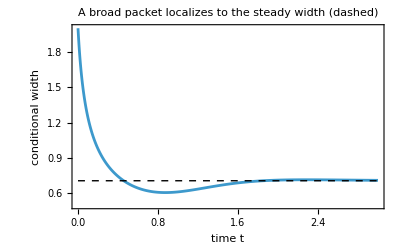

```mathematica
ListLinePlot[widthsF, PlotRange -> {.5, All}, DataRange -> {0, nt dt}, Frame -> True,
 FrameLabel -> {"time t", "conditional width"},
 PlotLabel -> "A broad packet localizes to the steady width (dashed)",
 Epilog -> {Dashed, Line[{{0, (hbar/(4 λR mass))^(1/4)}, {nt dt, (hbar/(4 λR mass))^(1/4)}}]}]
```

The norm sits at 1 by construction, every factor in the step being unitary or explicitly normalized, so its residual reports only floating-point health:

```mathematica
normError[Last@statesF]
```

0.

The checks with content are edgeMass and tailMass from Part II. Take their worst values over the run, one axis at a time. First the position leakage: the largest share of probability that ever reaches the outer tenth of the box, which stays negligible only while the packet never feels the glued seam of the ring.

```mathematica
Max[edgeMass[gF, #] & /@ statesF]
```

1.57891×10^-29

Then the momentum leakage: the largest share that ever reaches the fastest tenth of the momenta, which stays negligible only while the packet never reaches the top of the momentum ladder.

```mathematica
Max[tailMass[gF, #] & /@ statesF]
```

7.94292×10^-31

Both stay negligible: the packet never learns that the box is a ring or that the momentum ladder has a top rung. One bias does hide in the width plot: the terminal width sits slightly above the prediction, and it is worth splitting into its two parts. The approach to the steady width is a Riccati transient that dies at the rate 2 √(λℏ/m), not quite dead at the plotted time; and the step applies measurement and drift in sequence when in truth they share the interval, which shifts the discrete steady width by an offset first order in dt. The width is deterministic here (the free Riccati flow, blind to the record), so both parts are cleanly measurable: run to twice the time, killing the transient, and halve the step:

```mathematica
widthBias[dtq_, tf_] := Sqrt@xVar[gF, Last@BlockRandom[SeedRandom[11];
      trajectory[gF, 0 &, λR, dtq, Round[tf/dtq]][gaussian[gF, 0., 0., 2.]]]] - (hbar/(4 λR mass))^(1/4);
```

The offset is first order in the step, so halving the step should roughly halve it: the offset at the full step divided by the offset at the half step should come out near two.

```mathematica
widthBias[dt, 6.]/widthBias[dt/2, 6.]
```

1.99676

The surviving offset halves with the step: pure splitting bias, first order exactly as Part II promised, and none of it physics.

At unit detection efficiency the conditional state stays pure, which is what lets us carry it as a single state vector; the state only becomes mixed when we average over the noise, which is the master equation, coming next.

To average, we need the unconditional state as a density matrix ρ. Discarding the record and averaging the conditional states over the Wiener noise gives the Lindblad master equation, which integrates by the same operator split: the measurement dissipator damps each element ρ_ij by the factor e^(-λ/2(x_i-x_j)^2 dt), and the Hamiltonian acts as evolveStep turned into a matrix. Define the damping factor first:

```mathematica
decohereMat[g_, λ_, dt_] := Exp[-(λ/2) Outer[Subtract, g["x"], g["x"]]^2 dt];
```

Turn evolveStep into a matrix by applying it to each basis vector, materializing the very map the trajectories run so that conditional and unconditional dynamics share one drift by construction, and assemble one master-equation step in the same symmetric pattern as the wavefunction step, half the damping on each side of the unitary:

```mathematica
uniMat[g_, Vfun_, dt_] := Transpose[evolveStep[g, Vfun, dt] /@ IdentityMatrix[g["n"]]];
lindbladStep[g_, Vfun_, λ_, dt_] := With[{u = uniMat[g, Vfun, dt], dec = decohereMat[g, λ, dt/2]},
   Function[ρ, dec (u . (dec ρ) . ConjugateTranspose[u])]];
```

Each factor is exact, the damping being the dissipator's own flow and the unitary the Strang drift, so the symmetric sandwich keeps the deterministic step second order in dt.

Position observables read straight off ρ's diagonal, but momentum observables like ⟨(p̂)^2⟩ need the momentum-squared operator as a matrix, built spectrally as F^† diag(p^2) F with F the transform matrix:

```mathematica
p2Op[g_] := With[{fm = FourierMatrix[g["n"], FourierParameters -> {0, -1}]},
   ConjugateTranspose[fm] . (g["p"]^2 fm)];
```

The same momentum diagonal also gives the momentum-tail leakage of a density matrix, the ρ-version of tailMass: it feeds the shared helper the momentum-basis diagonal pρp in place of ψ_p^2. We define it here, beside the other matrix tools, and use it in Part V once the master equation is run far past the grid's comfort:

```mathematica
ρpTail[g_, ρ_] := With[{fm = FourierMatrix[g["n"], FourierParameters -> {0, -1}]},
   outerTenth[g["p"], Re@Diagonal[fm . ρ . ConjugateTranspose[fm]]]];
```

Now the second known fact, the measurement backaction. Work on a small 32-point grid over a box of width 16:

```mathematica
gS = grid[32, 16.];
```

Use a fine step and a short total time:

```mathematica
dtS = 0.0005; tf = 0.4; ntS = Round[tf/dtS];
```

Start from a single narrow packet at the origin:

```mathematica
ψ0 = gaussian[gS, 0., 0., 1.];
```

Propagate the free master equation from that packet, carried now as a density matrix ρ:

```mathematica
ρfree = NestList[lindbladStep[gS, 0 &, λR, dtS], projector[ψ0], ntS];
```

Calculate (p̂)^2:

```mathematica
p2S = p2Op[gS];
```

The prediction is the initial momentum variance plus the steady gain, ⟨(p̂)^2⟩_0+λ ℏ^2 t_f:

```mathematica
predP2 = Re[Conjugate[ψ0] . p2S . ψ0] + λR hbar^2 tf;
```

Plot the momentum variance ⟨(p̂)^2⟩(t) climbing to that value (dashed):

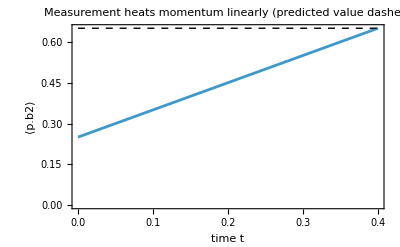

```mathematica
ListLinePlot[Re@Tr[# . p2S] & /@ ρfree, DataRange -> {0, tf}, Frame -> True,
 FrameLabel -> {"time t", "⟨p.b2⟩"}, PlotLabel -> "Measurement heats momentum linearly (predicted value dashed)",
 Epilog -> {Dashed, Line[{{0, predP2}, {tf, predP2}}]}]
```

And the endpoint lands on the prediction to integrator precision, because the ramp is exact for this split: the damping flow adds exactly λ ℏ^2 dt to ⟨(p̂)^2⟩ per step and the free drift conserves it:

```mathematica
Abs[Re@Tr[Last[ρfree] . p2S] - predP2]
```

4.26215×10^-13

The momentum variance rises exactly as ⟨(p̂)^2⟩_0+λ ℏ^2 t: position measurement feeds momentum at the constant rate λ ℏ^2, the price the uncertainty principle charges for position information. That rate is state- and Hamiltonian-independent, so for the free particle, whose Ĥ commutes with (p̂)^2, it is the whole story. In a potential it is not: the force couples ⟨(p̂)^2⟩ to ⟨(x̂)^2⟩ as the packet swings, which is why Part V follows the total energy instead. This backaction is the one piece of physics common to every case below; we meet it again competing with the trap.

As another example, let's consider a delocalized initial state. Take a "cat," a superposition of two packets sitting at x=±6. Set up a fresh grid, a moderate strength, and the two lobe centers:

```mathematica
gC = grid[256, 50.]; λC = 0.1; dtC = 0.005; {xL, xR} = {-6., 6.};
```

Build the cat as the normalized sum of a left packet and a right packet:

```mathematica
ψCat = Normalize[gaussian[gC, xL, 0., 1.] + gaussian[gC, xR, 0., 1.]];
```

Look at its two lobes:

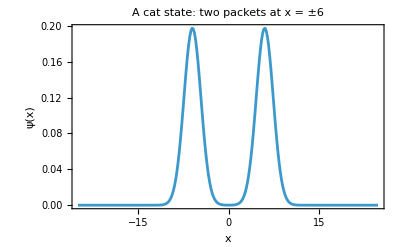

```mathematica
ListLinePlot[ψCat, DataRange -> {gC["x"][[1]], gC["x"][[-1]]}, Frame -> True,
 FrameLabel -> {"x", "ψ(x)"}, PlotLabel -> "A cat state: two packets at x = ±6"]
```

Its initial variance is large, dominated by that ±6 lobe separation:

```mathematica
xVar[gC, ψCat]
```

37.

Now watch the measurement collapse it. Take a moderate strength λ=0.1, chosen so the two lobes coexist for a visible stretch before one wins rather than collapsing in the first few steps, and run one trajectory:

```mathematica
statesC = BlockRandom[SeedRandom[5]; trajectory[gC, 0 &, λC, dtC, 600][ψCat]];
```

See the collapse as a surface of the conditional density (ψ(x,t))^2 over position and time. First pick the central band of the grid to plot, the window where the packets live:

```mathematica
band = Flatten@Position[UnitStep[10 - Abs[gC["x"]]], 1];
```

Then raise the density over position and time:

```mathematica
ListPlot3D[(Abs[statesC]^2)[[1 ;; ;; 6, band]], PlotRange -> All,
 DataRange -> {gC["x"][[{First@band, Last@band}]], {0, 3.}},
 ColorFunction -> (ColorData["DarkRainbow"][#3] &), Mesh -> None,
 AxesLabel -> {"x", "t", "|ψ|.b2"}, PlotLabel -> "A cat collapses to one packet"]
```

-Graphics3D-

The two ridges compete and one grows while the other fades, with no potential in sight.

That surface is the simulated conditional density, which no single run of an experiment can read out. What an observer holds is the stream of noisy outcomes (x̄)_k, and from it alone they must infer which lobe won. That inference is a running bet between two hypotheses, the left lobe at x_L=-6 against the right at x_R=+6, a deliberate coarse-graining that treats each lobe as a point at its center and ignores its width and motion. Each outcome has likelihood ∝e^(-2λ dt((x̄)_k-x_h)^2) under hypothesis h, so the log-odds for left over right accumulate one term at a time: each term is -2λ dt times ((x̄)_k+6)^2-((x̄)_k-6)^2, which is exactly 24 (x̄)_k, so the increment is simply -48λ dt (x̄)_k. Once a lobe has won and the readings center on it, the increment's mean is 288λ dt in the winner's favor, the distinguishability rate 2λ(Δx)^2 dt of Part I at lobe separation Δx=12. Rerun the same trajectory and keep both the conditional states and its stream of outcomes:

```mathematica
{catStates, {catOuts}} = BlockRandom[SeedRandom[5]; Reap[trajectory[gC, 0 &, λC, dtC, 600][ψCat]]];
```

Each outcome contributes a log-odds increment, left lobe against right; define it:

```mathematica
logOdds[xb_] := -2 λC dtC ((xb - xL)^2 - (xb - xR)^2);
```

Accumulate those increments and turn the running total into the posterior probability for the left lobe:

```mathematica
PleftRec = LogisticSigmoid[Accumulate[logOdds[catOuts]]];
```

First look at the raw stream the detector logs, the signal buried in noise:

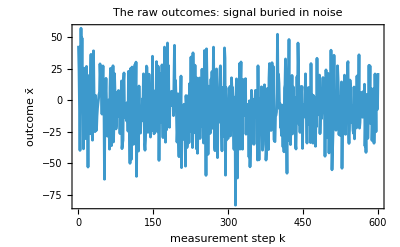

```mathematica
ListLinePlot[catOuts, PlotRange -> All, Frame -> True,
 FrameLabel -> {"measurement step k", "outcome x̄"},
 PlotLabel -> "The raw outcomes: signal buried in noise"]
```

That raw stream is almost pure noise: each reading scatters with standard deviation 1/√(4λ dt), far wider than the ±6 lobe separation, so no single outcome names the lobe. The verdict lives only in the slow average that PleftRec accumulates, which the grid's own final ⟨x̂⟩ should confirm, ending negative for the left lobe:

```mathematica
xMean[gC, Last@catStates]
```

-7.05318

So the outcomes say left lobe and the grid agrees. The road there is the instructive part: the belief builds only over many steps, and can even lean the wrong way first. For the comparison, first read the exact left-lobe mass the grid state carries at each step, which the observer never sees:

```mathematica
PleftGrid = Total@Pick[Abs[#]^2, UnitStep[(xL + xR)/2 - gC["x"]], 1] & /@ catStates;
```

Plot the observer's posterior forming over the first many steps, from the even prior 1/2, beside that hidden grid mass:

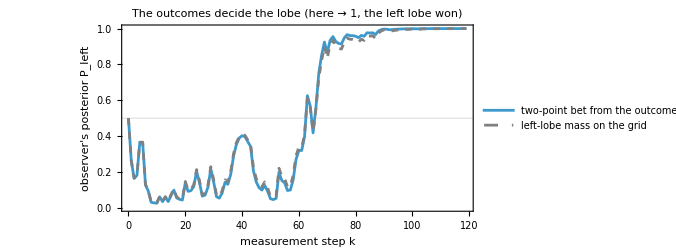

```mathematica
ListLinePlot[{Prepend[PleftRec, 0.5][[1 ;; 120]], PleftGrid[[1 ;; 120]]}, DataRange -> {0, 119},
 Frame -> True, ImageSize -> 500, AspectRatio -> 1/2, PlotRange -> {0, 1},
 GridLines -> {None, {{0.5, Gray}}}, PlotStyle -> {Automatic, Directive[Gray, Dashed]},
 PlotLegends -> {"two-point bet from the outcomes", "left-lobe mass on the grid"},
 FrameLabel -> {"measurement step k", "observer's posterior P_left"},
 PlotLabel -> "The outcomes decide the lobe (here → 1, the left lobe won)"]
```

Read the two curves by what an experiment could actually see. The solid curve is the two-point bet built from the noisy readings alone, so it is exactly what an observer holds: it starts at an even 1/2, wanders, at first even leans toward the wrong lobe, then climbs to 1 as reading after reading accumulates and the state localizes to the left lobe. The dashed curve is a different kind of thing. It is the true fraction of the packet sitting in the left lobe, read straight off the grid state itself, and no experiment can see that state, so this curve is not observable: it is drawn only as the hidden truth to check the bet against. The two-point bet rides right on it, and the small gap between them is the price of treating each lobe as a single point, which for deciding which lobe won costs almost nothing.

That verdict was this run's; a different noise history would decide differently. The initial cat is symmetric, so nothing favors either lobe: the measurement forces a definite choice, but which lobe is set entirely by the noise. Overlay several independent seeded runs and watch their posteriors split, some pinning to 1 (left), some to 0 (right):

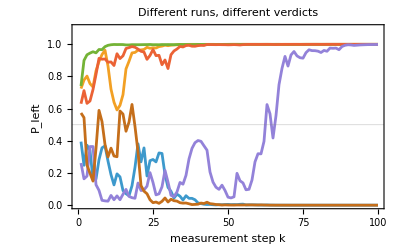

```mathematica
ListLinePlot[
 Table[BlockRandom[SeedRandom[k];
    LogisticSigmoid[Accumulate[logOdds[Reap[trajectory[gC, 0 &, λC, dtC, 100][ψCat]][[2, 1]]]]]], {k, 6}],
 PlotRange -> {0, 1.1}, Frame -> True, GridLines -> {None, {{0.5, Gray}}},
 FrameLabel -> {"measurement step k", "P_left"}, PlotLabel -> "Different runs, different verdicts"]
```

The runs split between the two lobes, each driven to a definite verdict by its own outcomes. This is the outcome stream doing the observer's inference, the same accumulation a real experiment performs in software beside the detector. Now we turn on a potential and ask what survives.

## Part IV: The Harmonic Trap: Position Sharper Than the Ground State

A trapped particle is never still: even in its ground state its position keeps the zero-point variance Σ_x^zp=ℏ/2mω, the ground state's own blur. So here is the question this Part answers: watch that position continuously, and can the conditional state become sharper in position than the ground state itself? What does the state become?

The harmonic trap is where this can be settled exactly. Because Ĥ=(p̂)^2/2m+1/2 m ω^2(x̂)^2 is quadratic, a conditional state that starts Gaussian stays Gaussian under both the measurement update and the evolution, so the whole state is five numbers: the two means ⟨x̂⟩,⟨p̂⟩ and the three covariances Σ_x=⟨(x̂)^2⟩-⟨x̂⟩^2, C=1/2⟨{x̂,p̂}⟩-⟨x̂⟩⟨p̂⟩, and Σ_p=⟨(p̂)^2⟩-⟨p̂⟩^2. We can solve their steady state with algebra before ever touching the grid. (This is also the real setting of cavity and levitated optomechanics, where light monitors a mechanical mode.)

Feed the trap Hamiltonian into the stochastic Schrödinger equation of Part I and apply it to each moment with Itô calculus. The equations of motion split cleanly in two. The two means follow the classical Hamilton drift plus a measurement gain acting on the record's noise:

d⟨x̂⟩=⟨p̂⟩/m dt+2 √λ Σ_x dW,    d⟨p̂⟩=-m ω^2⟨x̂⟩ dt+2 √λ C dW.

The three covariances follow a deterministic matrix Riccati flow, free of any dW:

(Σ̇)_x=(2C)/m-4λ Σ_x^2,    Ċ=Σ_p/m-m ω^2 Σ_x-4λ Σ_x C,    (Σ̇)_p=-2m ω^2 C+λ ℏ^2-4λ C^2.

The split is the whole reason the trap is solvable: the covariance rates depend only on the covariances, never on the means or the noise, so they close among themselves and run deterministically. Keeping λ,ω,m,ℏ symbolic, write the three rates as a vector:

```mathematica
ClearAll[Σx, Cc, Σp, λ, ω, m, ℏ, η, σ];
riccati = {2 Cc/m - 4 λ Σx^2, Σp/m - m ω^2 Σx - 4 λ Σx Cc, -2 m ω^2 Cc + λ ℏ^2 - 4 λ Cc^2}
```

{(2 Cc)/m-4 λ Σx^2,Σp/m-4 Cc λ Σx-m Σx ω^2,-4 Cc^2 λ-2 Cc m ω^2+λ ℏ^2}

Solve for the fixed point where all three rates vanish:

```mathematica
steady = SolveValues[Thread[riccati == 0], {Σx, Cc, Σp}] // FullSimplify
```

{{-(√(-(ω^2+(√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/m^2)/λ^2))/(2 √2),-(m^2 ω^2+√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(4 m λ),1/2 √((m^4 ω^4)/2+2 m^2 λ^2 ℏ^2) √(-(ω^2+(√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/m^2)/λ^2)},{(√(-(ω^2+(√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/m^2)/λ^2))/(2 √2),-(m^2 ω^2+√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(4 m λ),-1/2 √((m^4 ω^4)/2+2 m^2 λ^2 ℏ^2) √(-(ω^2+(√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/m^2)/λ^2)},{-√(-ω^2/(8 λ^2)+(√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(8 m^2 λ^2)),(-m^2 ω^2+√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(4 m λ),-1/2 √((m^4 ω^4)/2+2 m^2 λ^2 ℏ^2) √((-m^2 ω^2+√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(m^2 λ^2))},{√(-ω^2/(8 λ^2)+(√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(8 m^2 λ^2)),(-m^2 ω^2+√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(4 m λ),1/2 √((m^4 ω^4)/2+2 m^2 λ^2 ℏ^2) √((-m^2 ω^2+√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(m^2 λ^2))}}

SolveValues returns several algebraic roots; the physical one has Σ_x>0 and Σ_p>0. Write a symbolic test for those signs, one that must hold for all m,λ,ℏ>0 and ω≥0:

```mathematica
positiveQ[sol_] := TrueQ@Resolve[ForAll[{m, λ, ω, ℏ},
    m > 0 && λ > 0 && ω >= 0 && ℏ > 0,
    (sol[[1]] | sol[[3]]) ∈ Reals && sol[[1]] > 0 && sol[[3]] > 0], Reals];
```

Exactly one root passes it:

```mathematica
positiveQ /@ steady
```

{False,False,False,True}

Select that physical branch:

```mathematica
{ΣxSS, CcSS, ΣpSS} = SelectFirst[steady, positiveQ]
```

{√(-ω^2/(8 λ^2)+(√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(8 m^2 λ^2)),(-m^2 ω^2+√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(4 m λ),1/2 √((m^4 ω^4)/2+2 m^2 λ^2 ℏ^2) √((-m^2 ω^2+√(m^4 ω^4+4 m^2 λ^2 ℏ^2))/(m^2 λ^2))}

The first entry is the steady position variance Σ_x^ss=1/(2 √2)√((-m ω^2+√(4 ℏ^2 λ^2+m^2 ω^4))/(λ^2 m)). Two checks that it is right. First, perfect measurement keeps the state pure, and a pure Gaussian sits exactly at the uncertainty floor, so Σ_x Σ_p-C^2 must come out to ℏ^2/4:

```mathematica
Simplify[ΣxSS ΣpSS - CcSS^2, {λ > 0, ω > 0, m > 0, ℏ > 0}]
```

ℏ^2/4

Second, switching off the trap, ω→0, should return the free-particle steady value √(ℏ/4λm):

```mathematica
Simplify[Limit[ΣxSS, ω -> 0], {λ > 0, m > 0, ℏ > 0}]
```

1/2 √(ℏ/(m λ))

Both check out: the steady state is a pure Gaussian that reduces to the free particle when the trap is switched off.

Now the payoff, the question we opened with. Set the steady variance against the zero-point value Σ_x^zp=ℏ/2mω and simplify the ratio:

```mathematica
Simplify[ΣxSS/(ℏ/(2 m ω)), {λ > 0, ω > 0, m > 0, ℏ > 0}]
```

(ω √(m (-m ω^2+√(m^2 ω^4+4 λ^2 ℏ^2))))/(√2 λ ℏ)

In the single dimensionless measurement strength μ=2ℏλ/m ω^2, the above formula is exactly √(2(√(1+μ^2)-1))/μ.

Define a function, and the strength beside it:

```mathematica
sqRatio[u_] := Sqrt[2 (Sqrt[1 + u^2] - 1)]/u;
μ = 2 ℏ λ/(m ω^2);
```

And confirm the two forms agree:

```mathematica
Simplify[ΣxSS/(ℏ/(2 m ω)) == sqRatio[μ], {λ > 0, ω > 0, m > 0, ℏ > 0}]
```

True

That ratio is below 1 for every μ>0, and it strictly falls as you watch harder; both are theorems, not plot impressions. First, that the ratio stays below one at every strength, so the position is squeezed below the vacuum however gently you watch:

```mathematica
Resolve[ForAll[u, u > 0, sqRatio[u] < 1], Reals]
```

True

Second, that its slope is negative everywhere, so watching harder always squeezes the position further:

```mathematica
Resolve[ForAll[u, u > 0, D[sqRatio[u], u] < 0], Reals]
```

True

Its weak-measurement limit:

```mathematica
Asymptotic[sqRatio[u], {u, 0, 2}, Assumptions -> u >= 0]
```

1-u^2/8

And its strong-measurement limit:

```mathematica
Asymptotic[sqRatio[u], {u, Infinity, 1}, Assumptions -> u >= 0]
```

(√2)/(√u)

So the ratio is ≈1-μ^2/8 for weak watching and ≈√(2/μ) for strong, and the whole curve between those limits stays under the vacuum line:

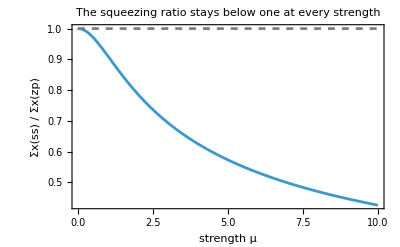

```mathematica
Plot[{sqRatio[u], 1}, {u, 0, 10}, Frame -> True, PlotStyle -> {Automatic, Directive[Gray, Dashed]},
 FrameLabel -> {"strength μ", "Σx(ss) / Σx(zp)"},
 PlotLabel -> "The squeezing ratio stays below one at every strength"]
```

There is the answer, stated plainly: continuous position measurement pushes the conditional variance below the zero-point at any strength μ>0, and deeper the harder you watch. The conditional state is a pure squeezed state, narrower in position than the ground state itself, because the measurement is steadily extracting position information.

Now put numbers to it. Fix a strongly-measured regime, ω=1 and λ=2 (so μ=4), and the vacuum scales that go with it:

```mathematica
ωR = 1.; λH = 2.;
ΣxZP = hbar/(2 mass ωR); ΣpZP = hbar mass ωR/2;
harmNum = {ℏ -> hbar, m -> mass, ω -> ωR, λ -> λH};
```

Read the steady position variance in units of the vacuum, the grid-substituted expression beside its exact closed form at μ=4; both land on the same number, and both fall below one:

```mathematica
{(ΣxSS /. harmNum)/ΣxZP, sqRatio[4]}
```

{0.624811,1/2 √(1/2 (-1+√17))}

It is below 1: sharper in position than the ground state. For momentum the opposite happens, anti-squeezed above its own zero-point value:

```mathematica
(ΣpSS /. harmNum)/ΣpZP
```

2.57616

The position is squeezed well below the zero-point and the momentum is anti-squeezed above it: the backaction paid for the position information. Notice the momentum pays more than the reciprocal of the position gain: the two ratios multiply to more than one. They must, because the steady state also carries the position-momentum correlation C, and the purity identity verified above rearranges into

Σ_x^ss/Σ_x^zp·Σ_p^ss/Σ_p^zp = 1+(2C/ℏ)^2.

Confirm it:

```mathematica
Simplify[(ΣxSS/(ℏ/(2 m ω))) (ΣpSS/(ℏ m ω/2)) == 1 + (2 CcSS/ℏ)^2, {λ > 0, ω > 0, m > 0, ℏ > 0}]
```

True

The reciprocal holds exactly only in a frame tilted to match the state's own spread; in the ordinary x and p directions the correlation C is what lifts the product above one, while the state stays exactly pure. All of this came from the closed-form moments. Does the grid, which never assumes the state stays a neat Gaussian, agree? Set up the trap potential and a grid:

```mathematica
Vharm = 0.5 mass ωR^2 #^2 &;
gH = grid[256, 24.]; dtH = 0.002; tfH = 3.; ntH = Round[tfH/dtH];
```

Evolve one trajectory from the ground state and take its conditional width over the run:

```mathematica
runH = BlockRandom[SeedRandom[11]; trajectory[gH, Vharm, λH, dtH, ntH][gaussian[gH, 0., 0., Sqrt[ΣxZP]]]];
ΣxH = xVar[gH, #] & /@ runH;
```

Plot it in units of the vacuum, against the closed-form Riccati value (red):

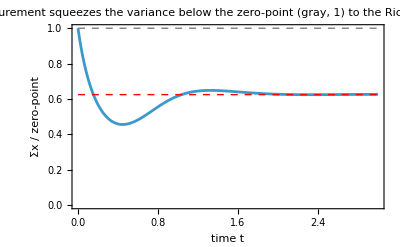

```mathematica
ListLinePlot[ΣxH/ΣxZP, DataRange -> {0, tfH}, PlotRange -> All, Frame -> True,
 Epilog -> {{Dashed, Gray, Line[{{0, 1}, {tfH, 1}}]},
   {Dashed, Red, Line[{{0, (ΣxSS /. harmNum)/ΣxZP}, {tfH, (ΣxSS /. harmNum)/ΣxZP}}]}},
 FrameLabel -> {"time t", "Σx / zero-point"},
 PlotLabel -> "Measurement squeezes the variance below the zero-point (gray, 1)
 to the Riccati value (red)"]
```

The grid variance relaxes to the Riccati steady value and sits well below the zero-point; the small remaining offset is the same first-order splitting bias Part III measured, independent of the grid spacing, and it shrinks with the step. The relaxation is the same in every run, because the conditional variance obeys a deterministic (noiseless) equation while only the mean is driven by the record.

The width plot compared just one number, Σ_x. Take the final step of the same run and compare the whole state: its position variance Σ_x, its momentum variance Σ_p, and their correlation C, each beside the value the algebra predicted:

```mathematica
Block[{ψf = Last[runH], ftψ, pm, sx, cc, sp},
  ftψ = ft[ψf];
  pm = gH["p"] . Abs[ftψ]^2;
  sx = xVar[gH, ψf];
  cc = Re[Conjugate[ψf] . (gH["x"] ift[gH["p"] ftψ])] - xMean[gH, ψf] pm;
  sp = gH["p"]^2 . Abs[ftψ]^2 - pm^2;
  TableForm[
   {{sx, ΣxSS /. harmNum, sx/(ΣxSS /. harmNum)},
    {cc, CcSS /. harmNum, cc/(CcSS /. harmNum)},
    {sp, ΣpSS /. harmNum, sp/(ΣpSS /. harmNum)},
    {sx sp - cc^2, N[hbar^2/4], (sx sp - cc^2)/(hbar^2/4)}},
   TableHeadings -> {{"Σx", "C", "Σp", "Σx Σp - C.b2"}, {"grid", "steady", "ratio"}}]]
```

| grid | steady | ratio
Σx | 0.313177 | 0.312405 | 1.00247
C | 0.391689 | 0.390388 | 1.00333
Σp | 1.28815 | 1.28808 | 1.00006
Σx Σp - C.b2 | 0.25 | 0.25 | 1.

Every grid value matches its predicted steady value to a fraction of a percent, the ratio column. The last row multiplies Σ_x by Σ_p and subtracts C^2: that combination equals ℏ^2/4 only for a pure state, and the grid hits it. So the grid, which never assumed the state was Gaussian, produces exactly the pure squeezed Gaussian the algebra predicted, not just the right width.

### Reading the Position Out of the Noise

The point of watching the particle is to know where it is. But the detector hands back something discouraging: a stream of position readings, each one almost pure noise. Can you recover the particle's mean position from that? You can, and the surprise is that you don't need the full wavefunction to do it, only five numbers, updated as each reading arrives. Those five numbers are themselves the conditional quantum state, its two means and three covariances; what you skip is the 256-amplitude grid, not the state. This five-number recipe is the quantum Kalman filter, the quantum form of the Kalman filter that turns a noisy signal into a running state estimate throughout engineering. It is what a trapped-nanoparticle or vibrating-membrane experiment does, inside a richer noise model: it never holds the full wavefunction, it watches the measured signal and runs this small calculation to know the mean position moment by moment.

Run one trajectory in the trap and keep every reading (x̄)_k the detector produces:

```mathematica
{recStates, {recOuts}} = BlockRandom[SeedRandom[21]; Reap[trajectory[gH, Vharm, λH, dtH, ntH][gaussian[gH, 0., 0., Sqrt[ΣxZP]]]]];
```

Also keep the conditional mean the full grid computes, the reference the filter is checked against later:

```mathematica
xGrid = xMean[gH, #] & /@ recStates;
```

Look at the readings on their own. Each scatters far wider than the conditional mean it carries, so the readings are mostly noise and the signal cannot be picked out by eye:

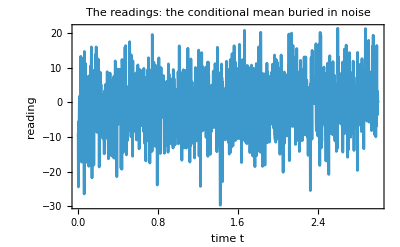

```mathematica
ListLinePlot[recOuts, DataRange -> {0, tfH}, PlotRange -> All, Frame -> True,
 FrameLabel -> {"time t", "reading"}, PlotLabel -> "The readings: the conditional mean buried in noise"]
```

The conditional mean ⟨x̂⟩ comes out not by averaging the noise away but through the filter, which carries five numbers: its estimates of the mean position ⟨x̂⟩ and mean momentum ⟨p̂⟩, and three more, Σ_x, Σ_p, and their correlation C, measuring how uncertain those estimates are. It updates all five at each reading, but the two kinds behave differently: the three uncertainty numbers follow a rule that never looks at the readings, set only by the trap and the measurement rate, so their whole path is fixed in advance and the same in every run, while the readings move only the two estimates. In one step all five advance by the same Euler-Maruyama update, a drift times Δt plus a gain times the filter's surprise Δ W_f:

Δ(⟨x̂⟩
⟨p̂⟩
Σ_x
C
Σ_p)=(⟨p̂⟩/m
-m ω^2⟨x̂⟩
2C/m-4λ Σ_x^2
Σ_p/m-m ω^2 Σ_x-4λ Σ_x C
-2m ω^2 C+λ ℏ^2-4λ C^2)Δt+(2 √λ Σ_x
2 √λ C
0
0
0)Δ W_f

The gain is nonzero only on the two means, so the readings move them and never the spreads. The last three rows of the drift are the covariance block, exactly the symbolic Riccati of this Part with the numbers substituted, so one definition serves both the algebra and the filter:

```mathematica
covDrift = Function[{Σx, Cc, Σp}, Evaluate[riccati /. harmNum]];
```

The surprise itself, the innovation, is the newest reading minus what the estimate predicted, and it reduces to the outcome and the step alone:

Δ W_f=Δ Y_k-2 √λ ⟨x̂⟩ Δt,    Δ Y_k=2 √λ Δt (x̄)_k ⟹ Δ W_f=2 √λ Δt ((x̄)_k-⟨x̂⟩),

Substitute that innovation back and every increment is proportional to Δt: the noise term folds into the drift, the two means picking up the measurement gain times the reading's offset (x̄)_k-⟨x̂⟩, the covariances keeping only their deterministic terms,

Δ(⟨x̂⟩
⟨p̂⟩
Σ_x
C
Σ_p)=(⟨p̂⟩/m+4λ Σ_x((x̄)_k-⟨x̂⟩)
-m ω^2⟨x̂⟩+4λC((x̄)_k-⟨x̂⟩)
2C/m-4λ Σ_x^2
Σ_p/m-m ω^2 Σ_x-4λ Σ_x C
-2m ω^2 C+λ ℏ^2-4λ C^2)Δt.

One step is that update:

```mathematica
filterStep[dtq_][{mx_, mp_, Σx_, Cc_, Σp_}, ΔYk_] := With[{dWf = ΔYk - 2 Sqrt[λH] mx dtq, cov = {Σx, Cc, Σp} + dtq covDrift[Σx, Cc, Σp]},
   Join[{mx + mp/mass dtq + 2 Sqrt[λH] Σx dWf, mp - mass ωR^2 mx dtq + 2 Sqrt[λH] Cc dWf}, cov]];
```

Build the record increment Δ Y_k the step consumes from the outcomes:

```mathematica
ΔY = 2 Sqrt[λH] dtH recOuts;
```

Run the filter along the whole record from the ground state, and keep its estimate of the conditional mean:

```mathematica
mFilter = FoldList[filterStep[dtH], {0., 0., ΣxZP, 0., ΣpZP}, ΔY][[All, 1]];
```

Compare that estimate with the grid's conditional mean, taking the largest gap between them as a fraction of the full range that mean covers over the run:

```mathematica
Max@Abs[mFilter - xGrid]/(Max@xGrid - Min@xGrid)
```

0.00165356

The gap is a tiny fraction of that range: the small price of finite time steps, not a real disagreement between the five numbers and the grid. From the noisy signal alone, five numbers recover the conditional mean that the full 256-point grid computed. Overlay them:

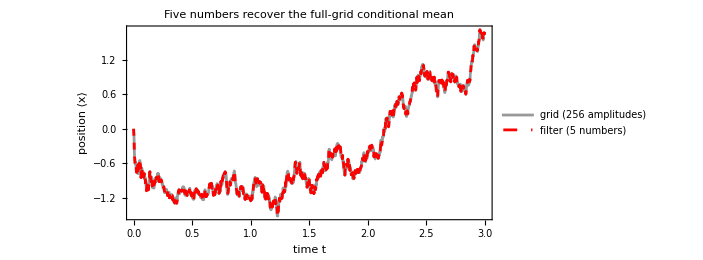

```mathematica
ListLinePlot[{Transpose[{dtH Range[0, ntH], xGrid}], Transpose[{dtH Range[0, ntH], mFilter}]},
 PlotStyle -> {Directive[Thick, GrayLevel[0.6]], Directive[Red, Dashed]}, Frame -> True, ImageSize -> 520,
 AspectRatio -> 1/2, PlotLegends -> {"grid (256 amplitudes)", "filter (5 numbers)"},
 FrameLabel -> {"time t", "position ⟨x⟩"},
 PlotLabel -> "Five numbers recover the full-grid conditional mean"]
```

The plot overlays two curves for the average position over time, and as with the lobe plot only one of them is something an experiment could actually draw. The red dashed curve is the estimate the five-number filter reports from nothing but the noisy stream of readings, so it is observable, the very quantity a real detector tracks. The gray curve is the average position carried by the full 256-amplitude wavefunction, and since no experiment holds that wavefunction it is not observable: it is drawn only as the reference to check the filter against, and the red lies right on top of it. The filter reaches it without ever building the wavefunction: it starts from the known initial state and, at each reading, nudges its running estimate by the surprise, how far the reading fell from what the estimate predicted, adjusting only its five numbers. So five numbers, driven by the raw signal alone, reproduce the average position that 256 complex amplitudes compute. That is what a real experiment does: to keep track of the particle's average position it never holds the wavefunction, it runs these five numbers in real time from the measured light, as a levitated nanoparticle or a vibrating membrane experiment does. Part III's outcomes answered a single yes-or-no question, which packet won; this one hands back the whole moving conditional mean.

### The Price of an Imperfect Detector

The perfect detector was a fiction. A real one catches only a fraction η of the light the particle scatters (η=1 is perfect, and it is a separate knob from the watching rate λ). This is the one gap between the below-the-vacuum result above and the laboratory: with this same machinery inside a fuller noise model, a levitated nanoparticle has been tracked to about 1.3 times its zero-point motion, wider than the vacuum rather than narrower. This section asks two plain questions and answers both. How much does the missing light blur the state, and what does that blur do to how tightly the position can be pinned.

Light that escapes detection still disturbs the particle (it gives it a kick) but carries away position information that you never get to see. So imperfect detection reduces the strength of the information you gain by a factor of η, while the physical backaction remains at the full measurement strength λ:

(Σ̇)_x=(2C)/m-4ηλ Σ_x^2,    Ċ=Σ_p/m-m ω^2 Σ_x-4ηλ Σ_x C,    (Σ̇)_p=-2m ω^2 C+λ ℏ^2-4ηλ C^2.

This is the earlier system with two numbers rescaled, λ→ηλ and ℏ→ℏ/√η, so the steady state we need comes straight from the one we already have:

```mathematica
{ΣxSSη, CcSSη, ΣpSSη} = {ΣxSS, CcSS, ΣpSS} /. {λ -> η λ, ℏ -> ℏ/Sqrt[η]};
```

How much the missing light blurs the state. The Robertson-Schrödinger relation sets a smallest joint spread in position and momentum: Σ_x Σ_p-C^2≥ℏ^2/4. That product is the position spread times the momentum spread less their correlation, and a perfect measurement holds it right at the floor. Read it on the lossy state:

```mathematica
Simplify[ΣxSSη ΣpSSη - CcSSη^2, {λ > 0, ω > 0, m > 0, ℏ > 0, 0 < η <= 1}]
```

ℏ^2/(4 η)

It comes out ℏ^2/4η, larger than the floor by 1/η, with λ, ω and m all gone: only the efficiency is left.

For a Gaussian state, the purity Tr(ρ^2) is ℏ/(2 √(Σ_x Σ_p-C^2)). For the stationary state above, it becomes:

```mathematica
Simplify[ℏ/(2 Sqrt[ΣxSSη ΣpSSη - CcSSη^2]), {ℏ > 0, 0 < η <= 1}]
```

√η

So the purity of the stationary state is the square root of the fraction of light you catch, and nothing else. For example, miss a tenth of it and you keep √0.9 of the purity, whatever the trap, whatever the particle, however hard you watch.

Let's compare the steady position spread with the ground state's (i.e. zero-point motion). Recall that μ is the measurement strength λ of the SDE made dimensionless by the trap, μ=2ℏλ/m ω^2, and that sqRatio gives the perfect-detector position spread in ground-state units. At efficiency η that ratio is Σ_x^ss(η)/Σ_x^zp= sqRatio[Sqrt[η] μ]/Sqrt[η]: it drops below 1, tighter than the ground state, only past a threshold watching strength. Solving the ratio =1 for that strength:

```mathematica
Simplify@Reduce[sqRatio[Sqrt[η] u]/Sqrt[η] <= 1 && u > 0 && 0 < η < 1, u, Reals]
```

0<η<1&&u≥2 √((1-η)/η^3)

that threshold being μ^*=2 √(1-η)/η^(3/2). A perfect detector pays nothing,

```mathematica
Limit[2 Sqrt[1 - η]/η^(3/2), η -> 1]
```

0

and a failing one pays without bound,

```mathematica
Asymptotic[2 Sqrt[1 - η]/η^(3/2), {η, 0, 1}, Assumptions -> 0 < η < 1]
```

2/η^(3/2)

So however inefficient the detector, as long as it catches some light you can still push the conditional position spread below the ground state's zero-point motion (narrower than the ground state) by watching hard enough; the worse it is, the larger the strength you need, growing without bound as η→0.

Plug the numbers we used and calculate the position spread:

```mathematica
sqRatio[Sqrt[η] μ]/Sqrt[η] /. harmNum /. η -> 0.34
```

1.28948

As one can see, it is more than one, wider than the vacuum rather than narrower.

Compute the strength it would have needed to reach the vacuum:

```mathematica
2 Sqrt[1 - η]/η^(3/2) /. η -> 0.34
```

8.19565

The threshold lands far above the strength we used, so the state sits above the vacuum because we watched below it, not because inefficiency forbids going under. A real experiment also carries thermal force noise and damping this model leaves out.

## Part V: Averaging Over Runs: A Trapped State That Never Settles

The conditional variance settled at its steady squeezed value. It is natural to expect the unconditional state, the average over the record, to settle too, perhaps into a thermal state. It does not, and seeing why is worth a moment. The trap conserves energy on its own, but the measurement backaction keeps injecting energy the closed trap has no way to remove. Watch this in the moments: the unconditional second moments close by themselves, and their energy has a constant source. Solve the unconditional moment equations in closed form and read the energy E(t):

```mathematica
ClearAll[XX, SS, PP];
usol = First@DSolve[{XX'[t] == 2 SS[t]/m, SS'[t] == PP[t]/m - m ω^2 XX[t],
    PP'[t] == -2 m ω^2 SS[t] + λ ℏ^2, XX[0] == xx0, SS[0] == 0, PP[0] == pp0}, {XX, SS, PP}, t];
energy = Simplify[PP[t]/(2 m) + (1/2) m ω^2 XX[t] /. usol]
```

(pp0+m^2 xx0 ω^2+t λ ℏ^2)/(2 m)

It is linear in t, so its time derivative should be a constant, the steady heating rate:

```mathematica
Simplify[D[energy, t]]
```

(λ ℏ^2)/(2 m)

The energy is exactly linear in time, E(t)=E_0+λ ℏ^2 t/2m, with no oscillatory part: the breathing of ⟨(x̂)^2⟩ and ⟨(p̂)^2⟩ against each other cancels in the sum, leaving only steady heating at dE/dt=λ ℏ^2/2m. That rate is not the trap's. The dissipator feeds energy at -λ/2⟨[x̂,[x̂,Ĥ]]⟩, and the double commutator is a pure number: [x̂,[x̂,Ĥ]]=[x̂,[x̂,(p̂)^2/2m]]=-ℏ^2/m, since x̂ commutes with V(x̂). So dE/dt=λ ℏ^2/2m in any potential: position measurement is a constant-power heater whatever the landscape, and the trap merely makes the bookkeeping solvable in closed form. Equivalently, the mean occupation climbs linearly, dn/dt=λℏ/2mω: the unconditional state is a mixed Gaussian whose energy and mean occupation grow without bound. With no damping and no detailed balance there is no thermodynamic temperature to assign, so it is thermal-like only in its Gaussian shape, not a thermal state. (The same closed solution with the trap switched off hands back the free particle of Part III:

```mathematica
Simplify[Limit[{XX[t], PP[t]} /. usol, ω -> 0]]
```

{xx0+(t^2 (3 pp0+t λ ℏ^2))/(3 m^2),pp0+t λ ℏ^2}

with the initial second moments as the constants xx0 and pp0: the momentum law of Part III drops out below, and above it the position variance grows as t^3 at late times, the momentum random walk integrated twice.) Confirm it on the grid by propagating the master equation and reading the energy and the individual moments at a few times. First two observables on ρ, position-squared as a diagonal expectation and the energy:

```mathematica
gHL = grid[96, 24.]; dtHL = 0.002; p2HL = p2Op[gHL];
x2Mean[g_, ρ_] := Re[Diagonal[ρ] . g["x"]^2];
Emeas[ρ_] := Re@Tr[ρ . p2HL]/(2 mass) + 0.5 mass ωR^2 x2Mean[gHL, ρ];
```

Now build the run from the ground state and tabulate. Start the density matrix from the trap ground state:

```mathematica
ρ0HL = projector[gaussian[gHL, 0., 0., Sqrt[ΣxZP]]];
```

Choose a handful of times to sample:

```mathematica
tsHL = {0., 0.5, 1., 1.5, 2.};
```

Propagate the master equation and snapshot ρ at each of those times:

```mathematica
ρsHL = With[{stp = lindbladStep[gHL, Vharm, λH, dtHL]},
   FoldList[Nest[stp, #1, Round[(#2[[2]] - #2[[1]])/dtHL]] &, ρ0HL, Partition[tsHL, 2, 1]]];
```

Tabulate the trace, the smallest eigenvalue of ρ (which stays nonnegative only while ρ is a genuine physical state, its populations never going negative), the energy, both second moments, and the purity at each time:

```mathematica
TableForm[{Re@Tr[#] & /@ ρsHL, Min[Re@Eigenvalues[#]] & /@ ρsHL, Emeas /@ ρsHL,
  x2Mean[gHL, #] & /@ ρsHL, Re@Tr[# . p2HL] & /@ ρsHL, Re@Tr[# . #] & /@ ρsHL},
 TableHeadings -> {{"tr ρ", "min eig", "E", "⟨x.b2⟩", "⟨p.b2⟩", "purity"}, tsHL}]
```

| 0. | 0.5 | 1. | 1.5 | 2.
tr ρ | 1. | 1. | 1. | 1. | 1.
min eig | -4.78243×10^-16 | -2.97766×10^-16 | -6.59754×10^-18 | 1.71174×10^-20 | 2.84465×10^-17
E | 0.5 | 1. | 1.5 | 2. | 2.5
⟨x.b2⟩ | 0.5 | 0.579265 | 1.04535 | 1.92944 | 2.8784
⟨p.b2⟩ | 0.5 | 1.42073 | 1.95465 | 2.07056 | 2.1216
purity | 1. | 0.569747 | 0.402659 | 0.288434 | 0.214705

As predicted, the trace holds at 1 and the spectrum stays nonnegative to roundoff. Of those two, positivity is the invariant with teeth: the step's very structure, a unit-diagonal damping inside a unitary sandwich, preserves the trace even for a wrong-signed kernel, while the spectrum would blow up instantly. The energy climbs in equal steps over 0≤t≤2, a straight ramp of slope exactly λ ℏ^2/2m; both ⟨(x̂)^2⟩ and ⟨(p̂)^2⟩ grow, and the purity falls from 1 as the unconditional state mixes. There is no steady state to plot, only a ramp:

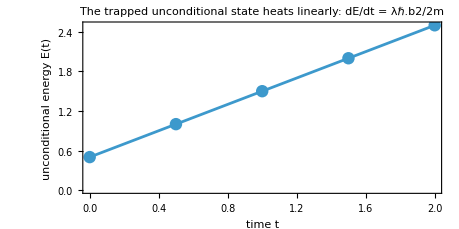

```mathematica
ListLinePlot[Transpose[{tsHL, Emeas /@ ρsHL}],
 Frame -> True, ImageSize -> 460, AspectRatio -> 1/2, PlotRange -> {0, All}, Mesh -> All,
 FrameLabel -> {"time t", "unconditional energy E(t)"},
 PlotLabel -> "The trapped unconditional state heats linearly: dE/dt = λℏ.b2/2m"]
```

Now set this beside Part IV, where the conditional variance froze at a squeezed value, and resolve the apparent contradiction. Both statements are true because the packet's center never settles: (⟨x̂⟩,⟨p̂⟩) is an undamped oscillator kicked by the record through the gains 2 √λ Σ_x and 2 √λ C of Part IV, and its excursions grow without bound even as the shape stays fixed. The heating lives entirely in that wandering. Once the covariance has settled, the Itô power the kicks feed into the center's energy, (2λ)/m C^2+2m ω^2 λ Σ_x^2, is exactly the Lindblad rate:

```mathematica
Simplify[2 λ CcSS^2/m + 2 m ω^2 λ ΣxSS^2 == λ ℏ^2/(2 m), {λ > 0, ω > 0, m > 0, ℏ > 0}]
```

True

So the division of labor is clean: the width holds the quantum uncertainty steady, the center performs the heating. (The free particle obeys the same bookkeeping: its steady C=ℏ/2 makes the momentum mean absorb 4λ C^2=λ ℏ^2 per unit time, which is the whole ramp of Part III.)

One scope note: the unbounded ramp is a statement about the continuum model, and the grid honors it only while the packet stays clear of the box edge and the momentum cutoff. Check the headroom on each axis. First the largest position squared the box can hold, the ceiling ⟨(x̂)^2⟩ would have to climb toward before the packet feels the box edge:

```mathematica
Max[Abs@gHL["x"]]^2
```

144.

Then the largest momentum squared the grid can hold, the ceiling ⟨(p̂)^2⟩ would have to climb toward before the packet reaches the top of the momentum ladder:

```mathematica
Max[Abs@gHL["p"]]^2
```

157.914

The tabulated moments sit fifty-fold or more below both bounds across this window; run long enough and any finite grid must eventually betray the ramp when the packet meets a cutoff. Watch that betrayal happen, on Part III's deliberately small free grid run far past its comfort. Run the free master equation for many thousands of steps:

```mathematica
ρlong = NestList[lindbladStep[gS, 0 &, λR, 0.002], projector[ψ0], 8000];
```

Plot the grid's momentum variance against the continuum ramp, which keeps climbing at λ ℏ^2 while the grid's momentum ladder tops out:

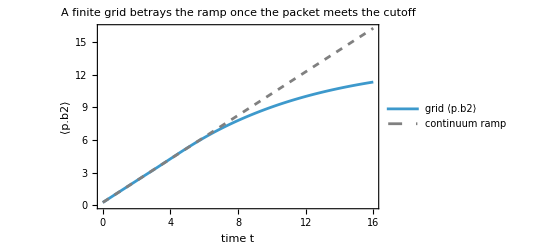

```mathematica
ListLinePlot[{Re@Tr[# . p2S] & /@ ρlong,
  Re[Conjugate[ψ0] . p2S . ψ0] + λR hbar^2 0.002 Range[0, 8000]},
 DataRange -> {0, 16.}, Frame -> True, PlotStyle -> {Automatic, Directive[Gray, Dashed]},
 PlotLegends -> {"grid ⟨p.b2⟩", "continuum ramp"}, FrameLabel -> {"time t", "⟨p.b2⟩"},
 PlotLabel -> "A finite grid betrays the ramp once the packet meets the cutoff"]
```

The two curves part company exactly when probability reaches the top of the momentum ladder, and ρpTail from Part III says so. At the start almost nothing sits in the fastest tenth of the momenta, so the grid is still faithful:

```mathematica
ρpTail[gS, First@ρlong]
```

1.40545×10^-16

By the end enough has piled into that momentum tail for the grid to break down, exactly where the two curves parted:

```mathematica
ρpTail[gS, Last@ρlong]
```

0.0724324

From there on the small grid is lying about the continuum, the honest content of every cutoff warning above. The trap's ramp, plotted before this caveat, sits inside its safe window, so it carries no such lie.

A genuine thermal steady state needs a mechanical damping channel to balance that input, which is exactly why the optomechanics experiments cool with feedback rather than watch the bare measurement; adding that channel to the master equation is the natural next extension.